```mathematica
Solve[(α1*ϵ)*(α2-ϵ)-(b-s*ϵ)^2*(2+2*Cos[k*a])==0, ϵ]
```

{{ϵ→(4 b s+α1 α2+4 b s Cos[a k]-√(-8 b^2 α1+8 b s α1 α2+α1^2 α2^2-8 b^2 α1 Cos[a k]+8 b s α1 α2 Cos[a k]))/(2 (2 s^2+α1+2 s^2 Cos[a k]))},{ϵ→(4 b s+α1 α2+4 b s Cos[a k]+√(-8 b^2 α1+8 b s α1 α2+α1^2 α2^2-8 b^2 α1 Cos[a k]+8 b s α1 α2 Cos[a k]))/(2 (2 s^2+α1+2 s^2 Cos[a k]))}}

```mathematica
Simplify[(4 b s+α1 α2+4 b s Cos[a k]-√(-8 b^2 α1+8 b s α1 α2+α1^2 α2^2-8 b^2 α1 Cos[a k]+8 b s α1 α2 Cos[a k]))/(2 (2 s^2+α1+2 s^2 Cos[a k]))]
```

(4 b s+α1 α2+4 b s Cos[a k]-√(α1 (-8 b^2+8 b s α2+α1 α2^2-8 b (b-s α2) Cos[a k])))/(2 (2 s^2+α1+2 s^2 Cos[a k]))

```mathematica
Simplify[(4 b s+α1 α2+4 b s Cos[a k]+√(-8 b^2 α1+8 b s α1 α2+α1^2 α2^2-8 b^2 α1 Cos[a k]+8 b s α1 α2 Cos[a k]))/(2 (2 s^2+α1+2 s^2 Cos[a k]))]
```

(4 b s+α1 α2+4 b s Cos[a k]+√(α1 (-8 b^2+8 b s α2+α1 α2^2-8 b (b-s α2) Cos[a k])))/(2 (2 s^2+α1+2 s^2 Cos[a k]))

```mathematica
s = (ⅇ^(-(a m (γ1+γ2))/(2 h^2)) γ1 √((m γ2)/h^2) (ⅇ^((a m γ1)/(2 h^2)) γ1-ⅇ^((a m γ2)/(2 h^2)) γ2))/(√((m γ1)/h^2) (γ1-γ2) (γ1+γ2))
```

-(4 ⅇ^2-8 ⅇ^4)/(6 √2 ⅇ^6)

```mathematica
α1 = (m*γ2)/h^2*(-1/2-γ1*ⅇ^(-m*γ2*a/h^2))
α2 = (m*γ1)/h^2*(-1/2-γ2*ⅇ^(-m*γ1*a/h^2))
b = (-m*γ1^2*s)/(2*h^2)-γ2*((m*√(γ1*γ2))/h^2*ⅇ^(-m*γ1*a/(2*h^2))*(1+ⅇ^(-m*γ2*a/h^2)))
```

8 (-1/2-4/ⅇ^8)

4 (-1/2-8/ⅇ^4)

-(32 √2 (1+1/ⅇ^8))/ⅇ^2+(2 √2 (4 ⅇ^2-8 ⅇ^4))/(3 ⅇ^6)

```mathematica
γ1 = 4 
γ2 = 8 
m = 1 
h = 1 
a = 1
```

4

8

1

1

1

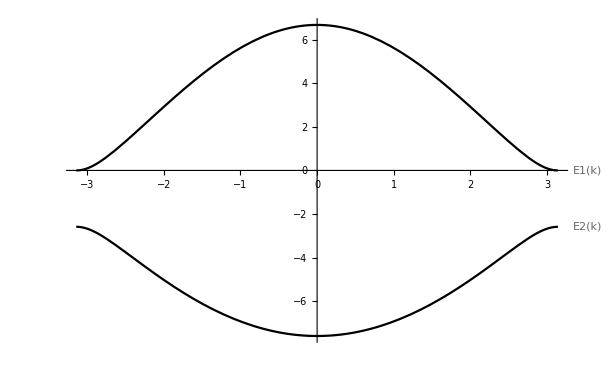

```mathematica
E1[k_]:=(4 b s+α1 α2+4 b s Cos[a k]-√(α1 (-8 b^2+8 b s α2+α1 α2^2-8 b (b-s α2) Cos[a k])))/(2 (2 s^2+α1+2 s^2 Cos[a k]))
E2[k_]:=(4 b s+α1 α2+4 b s Cos[a k]+√(α1 (-8 b^2+8 b s α2+α1 α2^2-8 b (b-s α2) Cos[a k])))/(2 (2 s^2+α1+2 s^2 Cos[a k]))












Plot[{E1[k],E2[k]},{k,-Pi/a,Pi/a},PlotLabels->"Expressions", PlotStyle->{Black,Black}]
```